```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY193_cloudy/sec_int_data/778nm.dat"]
```

{{1.46129,-0.102431},{1.36603,-0.0459078},{1.32759,-0.0555021},{1.2815,-0.0456566},{1.23231,-0.041145},{1.21009,-0.0392607},{1.18279,-0.0929051},{1.15809,-0.261689},{1.13892,-0.414804},{1.12738,-0.517364},{1.09219,-0.40579},{1.09146,-0.22842},{1.09503,-0.0430745},{1.10053,-0.00430927},{1.1079,-0.0172174},{1.12128,-0.0095656},{1.13179,-0.0111115},{1.14273,-0.0157128},{1.16583,-0.0164851},{1.1846,-0.0217141},{1.20387,0.02985},{1.22314,-0.0138048},{1.24682,-0.0136629}}

-0.607327+0.422764 x

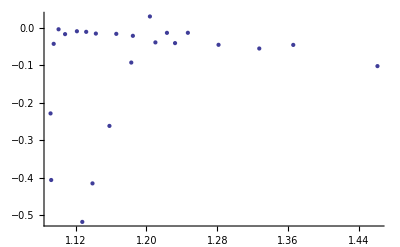

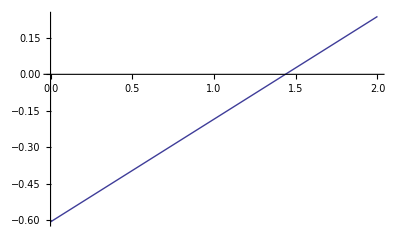

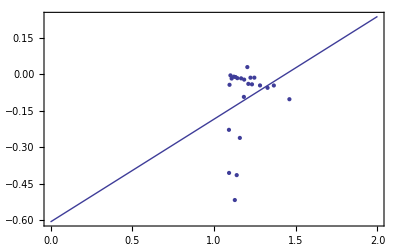

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```